## Preamble

This section contains the program’s pseudocode and a few definitions that should only need to be executed once (as long as the parameters are not changed).

## Pseudocode

Define the road network.

The network consists of a square grid of stops, with routes running N/S and E/W to define the grid (plus a dummy turnaround loop on each end). Between each pair of grid intersections we can also place stops.

Each stop is a node, whose coordinates we store.

We define arcs for each line, with slightly randomized travel times that depend on distance plus a constant boarding time.

Each stop is within walking distance of the four stops immediately adjacent, with walking times based on taxicab distance.

Define population centers and facilities.

Population centers are somewhat uniformly distributed, and each has coordinates and a population.

Facilities are somewhat clustered near the center.

All population centers and facilities receive walking arcs to their nearest stops depending on the grid square that they fall into. They can also be adjacent to each other if inside the same grid square.

Define OD and fleet sizes.

For each stop, decide the travel demand to all other stops according to a gamma distribution based on Euclidean distance.

The total outgoing travel demand for a stop should also depend on its population. For each stop, determine the nearest population center, and equally distribute the center’s population to all of its associated stops.

There should also be an overall scaling factor to adjust the daily traffic as a fraction of the overall population (my Chicago data shows that the number of daily boardings is approximately 2/3 of the total population).

The fleet sizes of each route should be proportional to the number of people using them, which can be quickly modeled by assuming that all of the travel demand travels along its shortest path.

Evaluate the objective function’s shape.

Pick several pairs of lines at random. For each pair, vary both of the fleet sizes within a range and calculate the objective value for each.

Use these results to generate a table of objective values, displayed as an array plot, in order to show how rough the objective looks.

## Function Definitions

These are functions required for every execution and should only need to be defined once.

```mathematica
(***)
```

## Parameters

The parameters defined below can be changed to generate different types of example network. Everything below this point should also be re-executed when the parameters are updated.

```mathematica
hlines=6;(* number of grid lines running horizontally *)
vlines=8;(* number of grid lines running vertically *)
hgap=0.0625;(* distance between horizontal lines (mi) *)
vgap=0.0625;(* distance between vertical lines (mi) *)
minbetween=0;(* minimum number of nodes to place between grid intersections *)
maxbetween=2;(* maximum number of nodes to place between grid intersections *)
wspeed=0.0455;(* pedestrian walking speed (mi/min) *)
minbspeed=0.3;(* minimum bus speed (mi/min) *)
maxbspeed=0.5;(* maximum bus speed (mi/min) *)
```

## Execution

The contents of the following sections may need to be repeatedly re-executed to generate satisfactory example networks.

## Network Construction

This section builds the underlying network of stops and other locations, along with the line arcs and walking arcs to connect them. A map of the network is shown once this process is complete.

```mathematica
(* Initialize data structures *)
ncoords={};(* list of node coordinates *)
ntype={};(* list of node types *)
nrows={};(* list of lists of node IDs for each street row *)
ncols={};(* list of lists of node IDs for each street column *)
arcs={};(* list of arcs, in i->j format *)
atype={};(* list of arc types *)
alines={};(* list of lists of arc IDs for each transit line *)

(* Generate grid intersection stops *)
ncoords=Flatten[Table[{vgap j,hgap i},{i,0,hlines-1},{j,0,vlines-1}],1];

(* Insert additional stops between grid intersections and build up the row/column lists *)
Module[{col,row,inc},
Do[
(* process each column from bottom to top *)
col={};(* node IDs in current column *)
Do[
col=Append[col,(i-1)+vlines (j-1)+1];(* current node ID *)
btw=RandomInteger[{minbetween,maxbetween}];(* number of stops to insert *)
inc=N[hgap/(btw+1)];(* distance north of current stop *)
Do[
(* insert stops between consecutive intersections *)
ncoords=Append[ncoords,ncoords[[(col[[-1]])]]+{0,inc}];(* new stop coordinate *)
col=Append[col,Length[ncoords]](* add new entry to column list *),
{k,1,btw}],
{j,1,hlines-1}];
(* topmost stop requires separate processing *)
col=Append[col,(i-1)+vlines (hlines-1)+1];(* top stop *)
ncols=Append[ncols,col](* add all stops in column to main column list *),
{i,1,vlines}];
Do[
(* process each row from left to right *)
row={};(* node IDs in current row *)
Do[
row=Append[row,vlines(i-1)+(j-1)+1];(* current node ID *)
btw=RandomInteger[{minbetween,maxbetween}];(* number of stops to insert *)
inc=N[vgap/(btw+1)];(* distance east of current stop *)
Do[
(* insert stops between consecutive intersections *)
ncoords=Append[ncoords,ncoords[[(row[[-1]])]]+{inc,0}];(* new stop coordinate *)
row=Append[row,Length[ncoords]](* add new entry to row list *),
{k,1,btw}],
{j,1,vlines-1}];
(* rightmost stop requires separate processing *)
row=Append[row,vlines i];(* right stop *)
nrows=Append[nrows,row](* add all stops in row to main row list *),
{i,1,hlines}];

ntype=ConstantArray[0,Length[ncoords]];(* stops are type 0 *)
];

(* Define line arcs for each column and row *)
Module[{head,tail},

Do[
(* process each column and generate arcs between each consecutive pair of stops *)
Do[
tail=


,
{j,1,Length[ncols[[i]]]-1}]

,
{i,1,Length[ncols]}];


atype=ConstantArray[0,Length[arcs]];(* line arcs are type 0 *)
];
```

```mathematica
ncoords
```

{{0.,0.},{0.0625,0.},{0.125,0.},{0.1875,0.},{0.25,0.},{0.3125,0.},{0.375,0.},{0.4375,0.},{0.,0.0625},{0.0625,0.0625},{0.125,0.0625},{0.1875,0.0625},{0.25,0.0625},{0.3125,0.0625},{0.375,0.0625},{0.4375,0.0625},{0.,0.125},{0.0625,0.125},{0.125,0.125},{0.1875,0.125},{0.25,0.125},{0.3125,0.125},{0.375,0.125},{0.4375,0.125},{0.,0.1875},{0.0625,0.1875},{0.125,0.1875},{0.1875,0.1875},{0.25,0.1875},{0.3125,0.1875},{0.375,0.1875},{0.4375,0.1875},{0.,0.25},{0.0625,0.25},{0.125,0.25},{0.1875,0.25},{0.25,0.25},{0.3125,0.25},{0.375,0.25},{0.4375,0.25},{0.,0.3125},{0.0625,0.3125},{0.125,0.3125},{0.1875,0.3125},{0.25,0.3125},{0.3125,0.3125},{0.375,0.3125},{0.4375,0.3125},{0.,0.09375},{0.,0.15625},{0.,0.208333},{0.,0.229167},{0.,0.270833},{0.,0.291667},{0.0625,0.0833333},{0.0625,0.104167},{0.0625,0.208333},{0.0625,0.229167},{0.0625,0.270833},{0.0625,0.291667},{0.125,0.0208333},{0.125,0.0416667},{0.125,0.15625},{0.125,0.208333},{0.125,0.229167},{0.125,0.270833},{0.125,0.291667},{0.1875,0.03125},{0.1875,0.09375},{0.1875,0.15625},{0.1875,0.21875},{0.25,0.0208333},{0.25,0.0416667},{0.25,0.0833333},{0.25,0.104167},{0.25,0.208333},{0.25,0.229167},{0.25,0.28125},{0.3125,0.03125},{0.3125,0.15625},{0.3125,0.21875},{0.3125,0.270833},{0.3125,0.291667},{0.375,0.03125},{0.375,0.09375},{0.4375,0.09375},{0.4375,0.145833},{0.4375,0.166667},{0.4375,0.21875},{0.4375,0.28125},{0.0833333,0.},{0.104167,0.},{0.208333,0.},{0.229167,0.},{0.34375,0.},{0.03125,0.0625},{0.0833333,0.0625},{0.104167,0.0625},{0.145833,0.0625},{0.166667,0.0625},{0.21875,0.0625},{0.0208333,0.125},{0.0416667,0.125},{0.0833333,0.125},{0.104167,0.125},{0.145833,0.125},{0.166667,0.125},{0.28125,0.125},{0.40625,0.125},{0.21875,0.1875},{0.270833,0.1875},{0.291667,0.1875},{0.333333,0.1875},{0.354167,0.1875},{0.40625,0.1875},{0.03125,0.25},{0.09375,0.25},{0.15625,0.25},{0.270833,0.25},{0.291667,0.25},{0.333333,0.25},{0.354167,0.25},{0.40625,0.25},{0.0833333,0.3125},{0.104167,0.3125},{0.15625,0.3125},{0.21875,0.3125},{0.270833,0.3125},{0.291667,0.3125},{0.333333,0.3125},{0.354167,0.3125},{0.395833,0.3125},{0.416667,0.3125}}

```mathematica
ncols
```

{{1,9,49,17,50,25,51,52,33,53,54,41},{2,10,55,56,18,26,57,58,34,59,60,42},{3,61,62,11,19,63,27,64,65,35,66,67,43},{4,68,12,69,20,70,28,71,36,44},{5,72,73,13,74,75,21,29,76,77,37,78,45},{6,79,14,22,80,30,81,38,82,83,46},{7,84,15,85,23,31,39,47},{8,16,86,24,87,88,32,89,40,90,48}}

```mathematica
nrows
```

{{1,2,91,92,3,4,93,94,5,6,95,7,8},{9,96,10,97,98,11,99,100,12,101,13,14,15,16},{17,102,103,18,104,105,19,106,107,20,21,108,22,23,109,24},{25,26,27,28,110,29,111,112,30,113,114,31,115,32},{33,116,34,117,35,118,36,37,119,120,38,121,122,39,123,40},{41,42,124,125,43,126,44,127,45,128,129,46,130,131,47,132,133,48}}

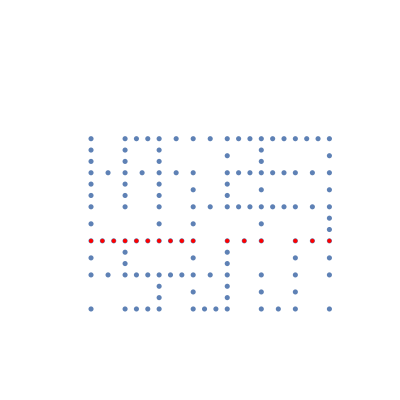

```mathematica
With[{set=nrows[[3]]},Show[ListPlot[ncoords,AspectRatio->1,PlotRange->{{-0.1,0.5},{-0.1,0.5}},Axes->False],Graphics[{Red,Point[ncoords[[set]]]}]]]
```